# Initialization

```mathematica
HaToeV=27.21138602;
```

```mathematica
SizeLegend=1.5;
```

```mathematica
SetDirectory["~/Dropbox/Manuscripts/CC4/Data"];
```

```mathematica
Needs["MaTeX`"]
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amssymb,amsmath,latexsym,amsfonts,amsthm,mathpazo,xcolor,bm,mhchem}"}];
```

# XLS

### Methods

```mathematica
Met={"CC2","CCSD","CCSDT-3","CC3","CCSDT","CC4","CCSDTQ","CCSDTQP"};
```

### MSE/AVDZ

```mathematica
MSEDZ=Import["CC4-Bench.xlsx"]⟦1,4;;28,3;;10⟧;
MSEDZ=Table[MSEDZ⟦a,b⟧-MSEDZ⟦a,Length[Met]⟧,{a,Length[MSEDZ]},{b,Length[Met]-1}];
Table[SetAccuracy[Mean[MSEDZ⟦;;,a⟧],4],{a,Length[Met]-1}]
Table[SetAccuracy[Mean[Abs[MSEDZ⟦;;,a⟧]],4],{a,Length[Met]-1}]
Table[SetAccuracy[Max[Abs[MSEDZ⟦;;,a⟧]],4],{a,Length[Met]-1}]
```

{0.02,0.075,0.03,0.013,0.0008,-0.0004,0.0004}

{0.257,0.109,0.04,0.028,0.018,0.003,0.002}

{0.575,0.324,0.196,0.152,0.047,0.011,0.007}

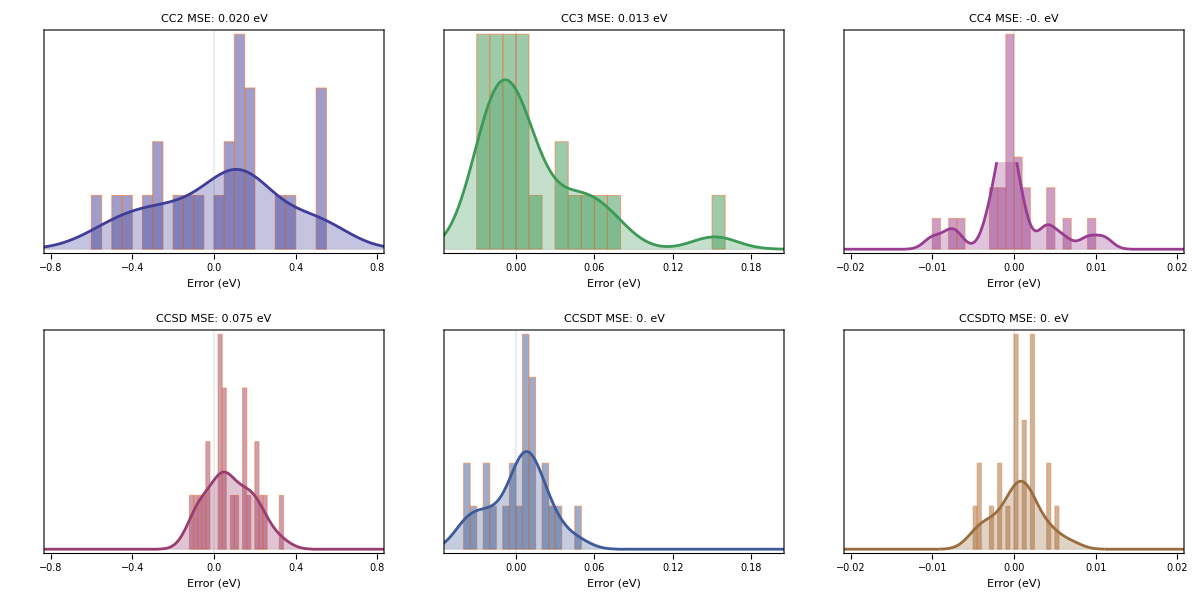

```mathematica
MSEDZ=Import["CC4-Bench.xlsx"]⟦1,4;;28,3;;10⟧;
MSEDZ=Table[MSEDZ⟦a,b⟧-MSEDZ⟦a,Length[Met]⟧,{a,Length[MSEDZ]},{b,Length[Met]-1}];
graph=Table[
Show[{
Histogram[MSEDZ⟦2;;,m⟧,20,"PDF",PlotTheme->"Scientific",BaseStyle->14,PlotRange->{{-0.1,0.1},Automatic},FrameLabel->{"Error (eV)",None},ChartStyle->{Directive[Opacity[0.5],ColorData[1,"ColorList"]⟦m⟧]},FrameTicks->{Automatic,None},PlotLabel->Style[Met⟦m⟧<>" MSE: "<>ToString[SetAccuracy[Mean[MSEDZ⟦;;,m⟧],4]]<>" eV",14]]
,
SmoothHistogram[DeleteCases[MSEDZ⟦2;;,m⟧,""],Automatic,"PDF",PlotRange->{{-1,1},Automatic},PlotStyle->Directive[ColorData[1,"ColorList"]⟦m⟧,Thickness[0.01]],Filling->Bottom,PlotTheme->"Web"]
},ImageSize->200]
,{m,Length[Met]-1}];
Grid[
{{Show[graph⟦1⟧,PlotRange->{{-0.8,0.8},All}],
Show[graph⟦4⟧,PlotRange->{{-0.05,0.2},All}],
Show[graph⟦6⟧,PlotRange->{{-0.02,0.02},All}]
}
,
{
Show[graph⟦2⟧,PlotRange->{{-0.8,0.8},All}],
Show[graph⟦5⟧,PlotRange->{{-0.05,0.2},All}],
Show[graph⟦7⟧,PlotRange->{{-0.02,0.02},All}]
}}
]
Export["histograms_MSE_AVDZ.pdf",%];
```

### MAE/AVDZ

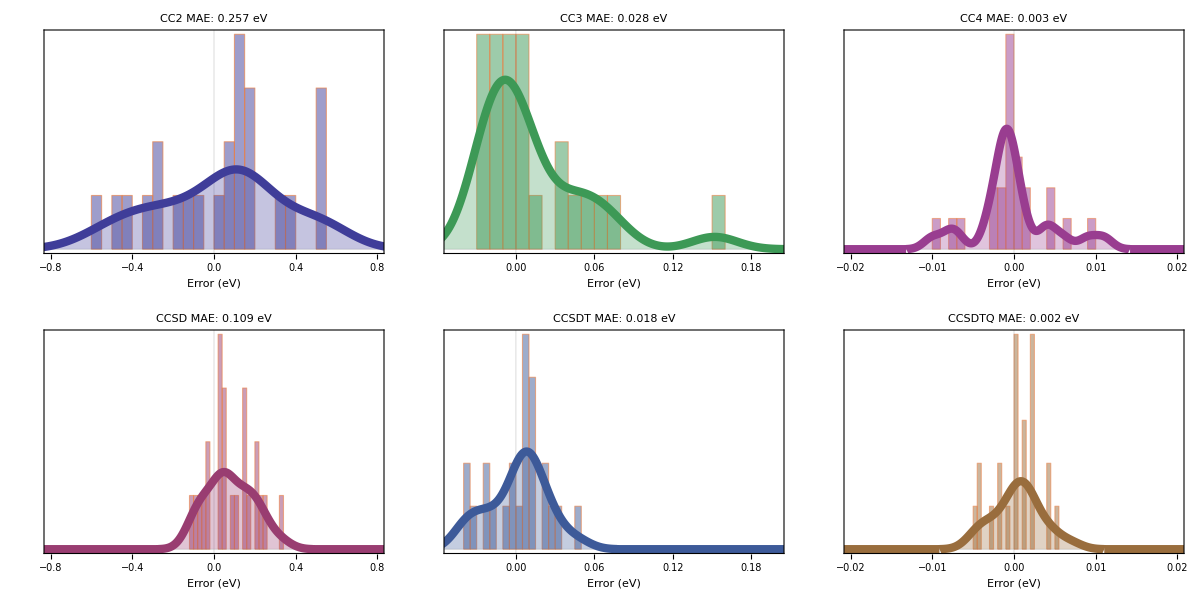

```mathematica
MAEDZ=Import["CC4-Bench.xlsx"]⟦1,4;;28,3;;10⟧;
MAEDZ=Table[MAEDZ⟦a,b⟧-MAEDZ⟦a,Length[Met]⟧,{a,Length[MAEDZ]},{b,Length[Met]-1}];
graph=Table[
Show[{
Histogram[MAEDZ⟦2;;,m⟧,20,"PDF",ChartBaseStyle->EdgeForm[Thick],PlotTheme->"Scientific",BaseStyle->14,PlotRange->{{-0.25,0.25},All},FrameStyle->Directive[Thick,20,Black],FrameLabel->{"Error (eV)",None},ChartStyle->{Directive[Opacity[0.5],ColorData[1,"ColorList"]⟦m⟧]},FrameTicks->{Automatic,None},PlotLabel->Style[Met⟦m⟧<>" MAE: "<>ToString[SetAccuracy[Mean[Abs[MAEDZ⟦;;,m⟧]],4]]<>" eV",20]]
,
SmoothHistogram[DeleteCases[MAEDZ⟦2;;,m⟧,""],Automatic,"PDF",PlotRange->{{-1,1},All},PlotStyle->Directive[ColorData[1,"ColorList"]⟦m⟧,Thickness[0.02]],Filling->Bottom,PlotTheme->"Web"]
},ImageSize->300]
,{m,Length[Met]-1}];
Grid[
{{Show[graph⟦1⟧,PlotRange->{{-0.8,0.8},All}],
Show[graph⟦4⟧,PlotRange->{{-0.05,0.2},All}],
Show[graph⟦6⟧,PlotRange->{{-0.02,0.02},All}]
}
,
{
Show[graph⟦2⟧,PlotRange->{{-0.8,0.8},All}],
Show[graph⟦5⟧,PlotRange->{{-0.05,0.2},All}],
Show[graph⟦7⟧,PlotRange->{{-0.02,0.02},All}]
}}
]
Export["histograms_MAE_AVDZ.pdf",%];
```

### Doubles

```mathematica
Doubles={
{3.107,2.632,2.341,2.241,2.213},
{3.283,2.874,2.602,2.521,2.503},
{5.247,4.756,4.454,4.424,4.397}
};
Doubles=Table[Doubles⟦a,b⟧-Doubles⟦a,5⟧,{a,3},{b,4}];
```

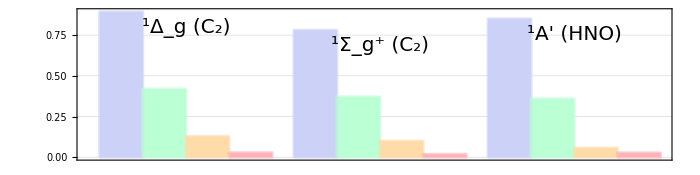

```mathematica
SizeFrameLabel=16;
Options$DNA={
PlotTheme->"Classic",
BarSpacing->{0,1/2},
Frame->True,
FrameStyle->Directive[Thick,20,Black],
ImageSize->700,
GridLines->{None,Automatic},
BaseStyle->20,
ChartBaseStyle->EdgeForm[Thickness[0.003]],
(*ImagePadding->{{All,All},{All,All}},*)
FrameTicks->{Automatic,Automatic},
(*PlotLabel->MaTeX["\\text{Ionization potentials from $G_0W_0$@PBE}",FontSize->SizeFrameLabel],*)
ChartLabels->{Placed[{Style["^1Δ_g (C_2)",20,FontFamily->"Times"],Style["^1Σ_g^+ (C_2)",20,FontFamily->"Times"],Style["^1A' (HNO)",20,FontFamily->"Times"]},Top],
Placed[{
Rotate[MaTeX["\\text{CC3}",FontSize->SizeFrameLabel],90 Degree],
Rotate[MaTeX["\\text{CCSDT}",FontSize->SizeFrameLabel],90 Degree],
Rotate[MaTeX["\\text{CC4}",FontSize->SizeFrameLabel],90 Degree],
Rotate[MaTeX["\\text{CCSDTQ}",FontSize->SizeFrameLabel],90 Degree]},Axis]},
FrameLabel->{None,MaTeX["\\text{Error wrt CCSDTQP (eV)}",FontSize->SizeFrameLabel]},
PlotRange->{Automatic,Automatic},
AspectRatio->1/4
};
BarChart[Doubles,Options$DNA]
Export["doubles.pdf",%];
```

# Composite method

```mathematica
Met={"CC2","CCSD","CC3","CCSDT","CC4","CCSDTQ","CCSDTQP"};
ΔE=Import["CC4-Bench.xlsx"]⟦1,4;;28,{3,4,6,7,8,9,10}⟧;
Ref=ΔE⟦;;,Length[Met]⟧;
ΔΔE=Table[ΔE⟦a,b⟧-Ref⟦a⟧,{a,Length[ΔE]},{b,Length[Met]-1}];
```

```mathematica
Table[{Met⟦b⟧,1/Length[ΔE]∑_(a=1)^Length[ΔE] Abs[ΔE⟦a,b⟧-Ref⟦a⟧]},{b,Length[Met]}]//TableForm
```

CC2 | 0.25652
CCSD | 0.1088
CC3 | 0.02796
CCSDT | 0.01768
CC4 | 0.00324
CCSDTQ | 0.00224
CCSDTQP | 0.

```mathematica
Table[{nMet,Minimize[1/(Length[ΔE]nMet)∑_(a=1)^Length[ΔE] Abs[∑_(b=1)^nMet Subscript[c, b] ΔE⟦a,b⟧-Ref⟦a⟧],Table[Subscript[c, b],{b,nMet}]]},{nMet,1,Length[Met]}]//TableForm
```

1 | 0.235771
c_1→0.989508
2 | 0.0336438 | 
c_1→-0.333655 | c_2→1.32719
3 | 0.00704452 |  | 
c_1→-0.0945742 | c_2→0.177027 | c_3→0.916487
4 | 0.00147788 |  |  | 
c_1→-0.0244118 | c_2→-0.168344 | c_3→-0.161263 | c_4→1.35553
5 | 0.00023653 |  |  |  | 
c_1→-0.00844998 | c_2→-0.0624675 | c_3→-0.00812754 | c_4→0.343232 | c_5→0.736281
6 | 0.000103759 |  |  |  |  | 
c_1→-0.000546859 | c_2→-0.0273444 | c_3→0.0202355 | c_4→-0.0037354 | c_5→0.13115 | c_6→0.880425
7 | 1.64619×10^-12 |  |  |  |  |  | 
c_1→2.34336×10^-11 | c_2→-3.13962×10^-10 | c_3→4.15701×10^-10 | c_4→-1.22928×10^-9 | c_5→-5.75167×10^-10 | c_6→1.81275×10^-8 | c_7→1.